# Understanding L = -mc^2

## Can we get away using exponential of the normal stuff?

## (#0): Notebook Preliminaries:

## (#0.1): Global Assumptions on Variables:

```mathematica
(* if you do this, then you don't have to keep specifying *)
$Assumptions={
c∈PositiveReals&&
xdot∈Reals&&
p∈Reals&&
β∈PositiveReals&&
m∈PositiveReals
};
```

## (#1): Showing the Nonrelativistic Limit of the Relativistic Lagrangian:

## (#1.1): The definition of the relativistic Lagrangian:

```mathematica
RelativisticLagrangian=-m c^2 √(1-xdot^2/c^2)
```

-c^2 m √(1-xdot^2/c^2)

## (#1.2): Expanding in the nonrelativistic limit, i.e. v<<c:

```mathematica
Series[RelativisticLagrangian,{xdot,0,2}]
```

-c^2 m+(m xdot^2)/2+O[xdot]^3

We see the second term is basically the one that matters here; it’s the nonrelativitic kinetic energy. The first term is the rest mass, but it doesn’t contribute to the nonrelativistic dynamics.

## (#2): Define the Exponential of the Relativistic Lagrangian:

## (#2.1): First choice: L = -m c^2 e^(-v^2/2 c^2)

```mathematica
ExoticRelativisticLagrangian=-m c^2 Exp[-xdot^2/(2 c^2)]
```

-c^2 ⅇ^(-xdot^2/(2 c^2)) m

```mathematica
Series[ExoticRelativisticLagrangian,{v,0,2}]
```

Series::ivar: c √(-ProductLog[-p^2/(c^2 m^2)]) is not a valid variable.

Series[-c^2 ⅇ^(-xdot^2/(2 c^2)) m,{c √(-ProductLog[-p^2/(c^2 m^2)]),0,2}]

## (#2.2): Second choice, which involves the wrong rest mass energy: L = -(m c^2)/2 e^(-v^2/c^2)

```mathematica
WrongRestMassRelativisticLagrangian=-(m c^2)/2 Exp[-xdot^2/c^2]
```

-1/2 c^2 ⅇ^(-xdot^2/c^2) m

```mathematica
Series[WrongRestMassRelativisticLagrangian,{v,0,2}]
```

Series::ivar: c √(-ProductLog[-p^2/(c^2 m^2)]) is not a valid variable.

Series[-1/2 c^2 ⅇ^(-xdot^2/c^2) m,{c √(-ProductLog[-p^2/(c^2 m^2)]),0,2}]

You can see it’s the wrong rest mass: m c^2/2 rather than m c^2. But, again, it’s a constant term in the Lagrangian, and doesn’t contribute to the nonrelativistic dynamics.

## (#3): Showing the nonrelativistic limits match to the desired order:

## (#3.1): Take the difference of the nonrelativistic limits for the “first choice Lagrangian”:

```mathematica
(Series[RelativisticLagrangian,{xdot,0,2}]-Series[ExoticRelativisticLagrangian,{xdot,0,2}])
```

O[xdot]^3

No difference to order v^3/c^3:

## (#3.2): Take the difference of the nonrelativistic limits for the “second choice Lagrangian”:

```mathematica
(Series[RelativisticLagrangian,{xdot,0,2}]-Series[WrongRestMassRelativisticLagrangian,{xdot,0,2}])
```

-(c^2 m)/2+O[xdot]^3

Difference is in the rest mass value.

## (#3.3): Expanding to higher orders:

```mathematica
(Series[RelativisticLagrangian,{xdot,0,8}]-Series[ExoticRelativisticLagrangian,{xdot,0,8}])
```

(m xdot^4)/(4 c^2)+(m xdot^6)/(24 c^4)+(m xdot^8)/(24 c^6)+O[xdot]^9

This sort of matters for the relativistic corrections to atoms via standard QM perturbation theory: https://en.wikipedia.org/wiki/Fine_structure#Relativistic_corrections

## (#4): Passing to the Hamiltonian:

## (#4.1): Use the standard relativistic Lagrangian:

### (#4.1.1): Find p := (∂L)/(∂v)

```mathematica
RelativisticConjugateMomentum=D[RelativisticLagrangian,xdot]
```

(m xdot)/(√(1-xdot^2/c^2))

### (#4.1.2): Solve for v:

```mathematica
RelativisticGeneralizedVelocity=Solve[p==RelativisticConjugateMomentum,xdot]
```

{{xdot→ConditionalExpression[(c p)/(√(c^2 m^2+p^2)), β>0&&c>0&&m>0&&p≤0]},{xdot→ConditionalExpression[(c p)/(√(c^2 m^2+p^2)), β>0&&c>0&&m>0&&p>0]}}

### (#4.1.3): Use the definition of the Hamiltonian with the proper substitutions:

```mathematica
RelativisticHamiltonian=FullSimplify[(p xdot-RelativisticLagrangian)/. RelativisticGeneralizedVelocity]
```

{ConditionalExpression[c √(c^2 m^2+p^2), p≤0],ConditionalExpression[c √(c^2 m^2+p^2), p>0]}

### (#4.1.4): Expand in small p:

Have to take the first result...

```mathematica
Series[c √(c^2 m^2+p^2),{p,0,6}]
```

c^2 m+p^2/(2 m)-p^4/(8 (c^2 m^3))+p^6/(16 c^4 m^5)+O[p]^7

Got the QM relativistic correction: -p^4/(8 c^2 m^3).

## (#4.2): Use the “first guess” for the Lagrangian:

### (#4.2.1): Find p := (∂L)/(∂v)

```mathematica
ExoticRelativisticConjugateMomentum=D[ExoticRelativisticLagrangian,xdot]
```

ⅇ^(-xdot^2/(2 c^2)) m xdot

### (#4.2.2): Solve for v:

#### (#4.2.2.1): Rely on Mathematica here:

```mathematica
ExoticRelativisticGeneralizedVelocity=Solve[p==ExoticRelativisticConjugateMomentum,xdot]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[p==ⅇ^(-xdot^2/(2 c^2)) m xdot,xdot]

Can’t be inverted easily. But I think the W-Function is here...

#### (#4.2.2.2): Rely on Algebra here:

```mathematica
ExoticRelativisticGeneralizedVelocity=√(-c^2 ProductLog[0,-p^2/(m^2 c^2)])
```

√(-c^2 ProductLog[-p^2/(c^2 m^2)])

#### (#4.2.2.3): Verify that the Algebra is right:

```mathematica
FullSimplify[ExoticRelativisticConjugateMomentum/.xdot->ExoticRelativisticGeneralizedVelocity]
```

c ⅇ^(1/2 ProductLog[-p^2/(c^2 m^2)]) m √(-ProductLog[-p^2/(c^2 m^2)])

Uh. Alright...

### (#4.2.3): Generate the Hamiltonian:

```mathematica
ExoticRelativisticHamiltonian=FullSimplify[(p xdot-ExoticRelativisticLagrangian)/. xdot->ExoticRelativisticGeneralizedVelocity]
```

c (c ⅇ^(1/2 ProductLog[-p^2/(c^2 m^2)]) m+p √(-ProductLog[-p^2/(c^2 m^2)]))

### (#4.2.4): Expand in small p:

```mathematica
Series[ExoticRelativisticHamiltonian,{p,0,4}]
```

c^2 m+(Abs[p] p)/m-p^2/(2 m)+(Abs[p] p^3)/(2 c^2 m^3)-(3 p^4)/(8 (c^2 m^3))+O[p]^5

```mathematica
Series[ExoticRelativisticHamiltonian,{p,0,4}]/.c->1
```

Piecewise[{{m-(3 p^2)/(2 m)-(7 p^4)/(8 m^3)+O[p]^5, p≤0}, {m+p^2/(2 m)+p^4/(8 m^3)+O[p]^5, True}}]

```mathematica
Series[ExoticRelativisticHamiltonian,{p,0,4}]/.c->1/.m->1
```

Piecewise[{{1-(3 p^2)/2-(7 p^4)/8+O[p]^5, p≤0}, {1+p^2/2+p^4/8+O[p]^5, True}}]

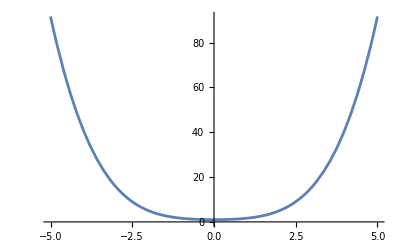

```mathematica
Plot[1+p^2/2+p^4/8,{p,-5,5}]
```